## Produce figures that illustrate how the standard Ramsey model changes when quadratic costs of adjustment to k are added

### Preamble (boring initialization stuff; ignore)

```mathematica
ClearAll["Global`*"];
Needs["PlotLegends`"];
If[Length[$FrontEnd] > 0, NBDir = SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[Length[$FrontEnd] == 0,SetDirectory["/Volumes/Data/Courses/Choice/LectureNotes/Growth/Handouts/qRamsey/Code/Mathematica/"]];

SetDirectory[NotebookDirectory[]];
SetOptions[Plot
,BaseStyle->{FontSize->16},PlotRange->All,Ticks->None,PlotStyle->{Thick}];
SetOptions[ListPlot
,BaseStyle->{FontSize->16},PlotRange->All,Ticks->None,PlotStyle->{Black,PointSize[Medium]}];
<<qRamseyFunctions.m;
{𝒸Color,𝒾Color,𝒿Color}={Darker[Green],𝒾Color=Red,𝒿Color=Black};
CostAdj0Thickness=Thickness[Medium];
CostAdjAltThickness=Thickness[Large];
```

## Policy Functions (measuring sensitivity to ω and ρ)

#### Zero adjustment cost ω (regular Ramsey model)

```mathematica
<<qRamseyParamsBase.m;
ω=0; (* ω measures size of cost of adjustment *)
Quiet[SolvePolFunc];(* Quiet[] supresses some error messages caused by ω=0 that do not actually signal a failed solution *)
{𝒸FuncAdjCost0,𝒾FuncAdjCost0,𝒿FuncAdjCost0}={𝒸Func,𝒾Func,𝒿Func};
```

#### Benchmark calibration

```mathematica
<<qRamseyParamsBase.m;
SolvePolFunc;
{𝒸FuncBase,𝒾FuncBase,𝒿FuncBase}={𝒸Func,𝒾Func,𝒿Func};
```

#### Calibration with huge costs of adjustment ω

```mathematica
<<qRamseyParamsBase.m;
ω=5*ωBase;
SolvePolFunc;
{𝒸FuncAdjCostHi,𝒾FuncAdjCostHi,𝒿FuncAdjCostHi}={𝒸Func,𝒾Func,𝒿Func};
```

Solid=No costs (standard Ramsey); Dashing=With high costs

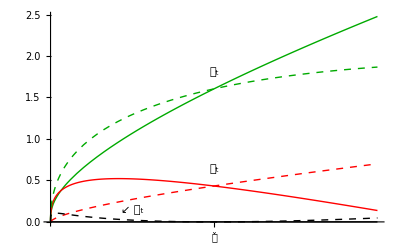

```mathematica
PolFuncAdjCost0VsHi=Show[Plot[{𝒸FuncAdjCost0[𝓀],𝒾FuncAdjCost0[𝓀],𝒿FuncAdjCost0[𝓀],𝒸FuncAdjCostHi[𝓀],𝒾FuncAdjCostHi[𝓀],𝒿FuncAdjCostHi[𝓀]},{𝓀,0,2𝓀SS}
,PlotStyle->{{CostAdj0Thickness,𝒸Color},{CostAdj0Thickness,𝒾Color},{CostAdj0Thickness,𝒿Color}
,{CostAdjAltThickness,Dashed,𝒸Color},{CostAdjAltThickness,Dashed,𝒾Color},{CostAdjAltThickness,Dashed,𝒿Color}}
,AxesLabel->{"𝓀_t"} ,Ticks->{{{𝓀SS,"𝓀̌"}},{}}],
Graphics[{
Text["𝒸_t",{𝓀SS,𝒸SS +.2}],
Text["𝒾_t",{𝓀SS,𝒾SS +.2}],
Text["↙ 𝒿_t",{𝓀SS/2,𝒾SS /3}]
}]
];

Print["Solid=No costs (standard Ramsey); Dashing=With high adj costs (q-Ramsey)"];Print[PolFuncAdjCost0VsHi];
```

```mathematica
Export["../../Figures/PolFuncAdjCost0VsHi.pdf",PolFuncAdjCost0VsHi];
Export["../../Figures/PolFuncAdjCost0VsHi.eps",PolFuncAdjCost0VsHi];
Export["../../Figures/PolFuncAdjCost0VsHi.png",PolFuncAdjCost0VsHi,ImageSize->{72 8.,72 8./GoldenRatio}];
```

Solid=Ramsey;Dashed=With baseline Adj Costs

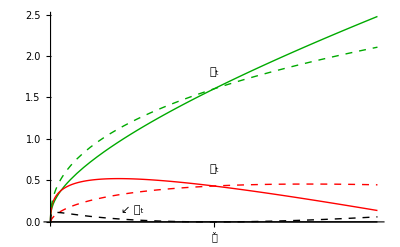

```mathematica
PolFuncAdjCost0VsBase=Show[Plot[{𝒸FuncAdjCost0[𝓀],𝒾FuncAdjCost0[𝓀],𝒿FuncAdjCost0[𝓀],𝒸FuncBase[𝓀],𝒾FuncBase[𝓀],𝒿FuncBase[𝓀]},{𝓀,0,2𝓀SS}
,PlotStyle->{{CostAdj0Thickness,𝒸Color},{CostAdj0Thickness,𝒾Color},{CostAdj0Thickness,𝒿Color}
,{CostAdjAltThickness,Dashed,𝒸Color},{CostAdjAltThickness,Dashed,𝒾Color},{CostAdjAltThickness,Dashed,𝒿Color}}
,AxesLabel->{"𝓀_t"} ,Ticks->{{{𝓀SS,"𝓀̌"}},{}}],
Graphics[{
Text["𝒸_t",{𝓀SS,𝒸SS +.2}],
Text["𝒾_t",{𝓀SS,𝒾SS +.2}],
Text["↙ 𝒿_t",{𝓀SS/2,𝒾SS /3}]
}]];
Print["Solid=Ramsey;Dashed=With baseline Adj Costs (q-Ramsey)"];Print[PolFuncAdjCost0VsBase];
```

```mathematica
Export["../../Figures/PolFuncAdjCost0VsBase.pdf",PolFuncAdjCost0VsBase];
Export["../../Figures/PolFuncAdjCost0VsBase.eps",PolFuncAdjCost0VsBase];
Export["../../Figures/PolFuncAdjCost0VsBase.png",PolFuncAdjCost0VsBase,ImageSize->{72 8.,72 8./GoldenRatio}];
```

#### Regular Ramsey model with log utility ρ=1 (solid) vs high ρ (Dashed lines)

```mathematica
<<qRamseyParamsBase.m;
ρ=3.;
ω=0;
Quiet[SolvePolFunc];
{𝒸FuncCostAdj0AndRRAHi,𝒾FuncCostAdj0AndRRAHi,𝒿FuncCostAdj0AndRRAHi}={𝒸Func,𝒾Func,𝒿Func};
```

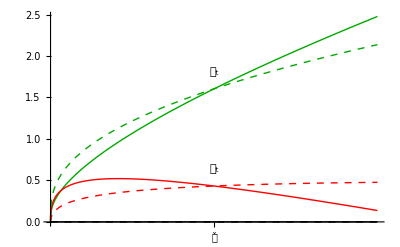

```mathematica
PolFuncRRALoVsHi=Show[
Plot[{𝒸FuncAdjCost0[𝓀],𝒾FuncAdjCost0[𝓀],𝒿FuncAdjCost0[𝓀],𝒸FuncCostAdj0AndRRAHi[𝓀],𝒾FuncCostAdj0AndRRAHi[𝓀],𝒿FuncCostAdj0AndRRAHi[𝓀]},{𝓀,0,2𝓀SS},PlotStyle->{{CostAdj0Thickness,𝒸Color},{CostAdj0Thickness,𝒾Color},{CostAdj0Thickness,𝒿Color},{Thick,Dashed,𝒸Color},{Thick,Dashed,𝒾Color},{Thick,Dashed,𝒿Color}},AxesLabel->{"𝓀_t"} ,Ticks->{{{𝓀SS,"𝓀̌"}},{}}],
Graphics[{
Text["𝒸_t",{𝓀SS,𝒸SS +.2}],
Text["𝒾_t",{𝓀SS,𝒾SS +.2}]}]];
Print[PolFuncRRALoVsHi];
```

```mathematica
Export["../../Figures/PolFuncRRALoVsHi.pdf",PolFuncRRALoVsHi];
Export["../../Figures/PolFuncRRALoVsHi.eps",PolFuncRRALoVsHi];
Export["../../Figures/PolFuncRRALoVsHi.png",PolFuncRRALoVsHi,ImageSize->{72 8.,72 8./GoldenRatio}];
```

## Impulse Response Functions (benchmark calibration)

### Permanent increase in Patience

```mathematica
<<qRamseyParamsBase.m;
ω=0;
Quiet[SolvePolFunc];
InitializeSimData;
Do[AddOnePeriod,{PreShockPeriods}];
β=0.98;
ω=0;
Quiet[SolvePolFunc];
Do[AddOnePeriod,{AfterShockPeriods}];
```

```mathematica
PatRiseAdjCost0=GraphicsGrid[{
{𝓀TimeAdjCost0=ListPlot[𝓀tList,AxesLabel->{"t","𝓀_t"},AxesOrigin->{0,0.Min[𝓀tList].95}],
λTimeAdjCost0=ListPlot[λtList,AxesLabel->{"t","λ_t"},AxesOrigin->{0,Min[λtList].95}]},
{𝒾TimeAdjCost0=ListPlot[𝒾tList,AxesLabel->{"t","𝒾_t"},AxesOrigin->{0,0.Min[𝒾tList].9}],
𝒸TimeAdjCost0=ListPlot[𝒸tList,AxesLabel->{"t","𝒸_t"},AxesOrigin->{0,0.Min[𝒸tList].95}]},{ℝTimeAdjCost0=ListPlot[ℝtp1List,AxesLabel->{"t","R_(t + 1)"},AxesOrigin->{0,Min[ℝtp1List].99}],𝒿TimeAdjCost0=ListPlot[𝒿tList,AxesLabel->{"t","𝒿_t"},AxesOrigin->{0,0}]
}},ImageSize->600];
(*
Print[PatRiseAdjCost0];
Export["../../Figures/PatRiseAdjCost0.pdf",PatRiseAdjCost0];
Export["../../Figures/PatRiseAdjCost0.eps",PatRiseAdjCost0];
Export["../../Figures/PatRiseAdjCost0.png",PatRiseAdjCost0,ImageSize->{72 8.,72 8./GoldenRatio}];
*)
```

```mathematica
<<qRamseyParamsBase.m;
Quiet[SolvePolFunc];
InitializeSimData;
Do[AddOnePeriod,{PreShockPeriods}];
β=0.98;
Quiet[SolvePolFunc];
Do[AddOnePeriod,{AfterShockPeriods}];
```

```mathematica
SetOptions[ListPlot,PlotStyle->{Red,PointSize[Medium]}];
PatRiseAdjCostBase=GraphicsGrid[{
{𝓀TimeAdjCostBase=ListPlot[𝓀tList,AxesLabel->{"t","𝓀_t"},AxesOrigin->{0,0.Min[𝓀tList].95}],
λTimeAdjCostBase=ListPlot[λtList,AxesLabel->{"t","λ_t"},AxesOrigin->{0,Min[λtList].95}]},
{𝒾TimeAdjCostBase=ListPlot[𝒾tList,AxesLabel->{"t","𝒾_t"},AxesOrigin->{0,0.Min[𝒾tList].9}],
𝒸TimeAdjCostBase=ListPlot[𝒸tList,AxesLabel->{"t","𝒸_t"},AxesOrigin->{0,0.Min[𝒸tList].95}]},{ℝTimeAdjCostBase=ListPlot[ℝtp1List,AxesLabel->{"t","R_(t + 1)"},AxesOrigin->{0,Min[ℝtp1List].99}],𝒿TimeAdjCostBase=ListPlot[𝒿tList,AxesLabel->{"t","𝒿_t"},AxesOrigin->{0,0}]
}},ImageSize->600];
SetOptions[ListPlot,PlotStyle->{Black,PointSize[Medium]}];
(*Print[PatRiseAdjCostBase];
Export["../../Figures/PatRiseAdjCostBase.pdf",PatRiseAdjCostBase];
Export["../../Figures/PatRiseAdjCostBase.eps",PatRiseAdjCostBase];
Export["../../Figures/PatRiseAdjCostBase.png",PatRiseAdjCostBase,ImageSize->{72 8.,72 8./GoldenRatio}];*)
```

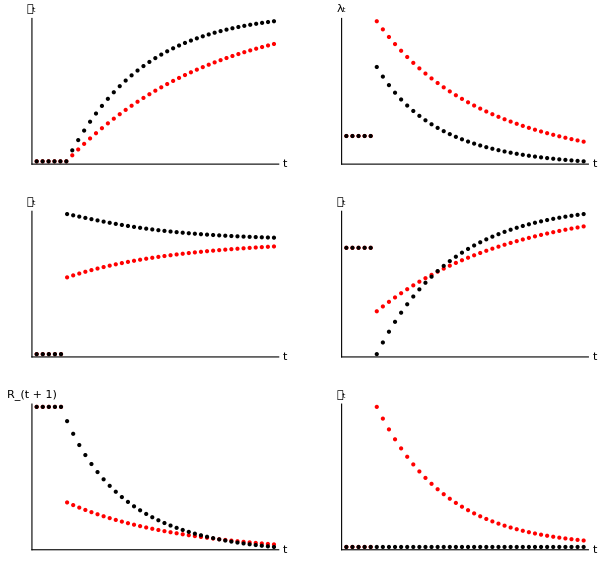

```mathematica
PatRiseCostAdj0VsBase=GraphicsGrid[{
{Show[𝓀TimeAdjCostBase,𝓀TimeAdjCost0],Show[λTimeAdjCostBase,λTimeAdjCost0]}
,{Show[𝒾TimeAdjCostBase,𝒾TimeAdjCost0],Show[𝒸TimeAdjCostBase,𝒸TimeAdjCost0]}
,{Show[ℝTimeAdjCostBase,ℝTimeAdjCost0],Show[𝒿TimeAdjCostBase,𝒿TimeAdjCost0]}
},ImageSize->600,PlotRange->All];
Print[PatRiseCostAdj0VsBase];
Export["../../Figures/PatRiseCostAdj0VsBase.pdf",PatRiseCostAdj0VsBase];
Export["../../Figures/PatRiseCostAdj0VsBase.eps",PatRiseCostAdj0VsBase];
Export["../../Figures/PatRiseCostAdj0VsBase.png",PatRiseCostAdj0VsBase,ImageSize->{72 8.,72 8./GoldenRatio}];
```

### 50 percent destruction of capital stock

```mathematica
<<qRamseyParamsBase.m;
ω=0; (* Basic Ramsey model first *)
Quiet[SolvePolFunc];
InitializeSimData;
Do[AddOnePeriod,{PreShockPeriods}];
𝓀tList[[-1]]=Last[𝓀tList]0.50; (* 50% of the capital is lost*)
Do[AddOnePeriod,{AfterShockPeriods}];
```

```mathematica
kDropCostAdj0=GraphicsGrid[{
{𝓀TimeCostAdj0=ListPlot[𝓀tList,AxesLabel->{"t","𝓀_t"},AxesOrigin->{0,0.Min[𝓀tList].95}],
λTimeCostAdj0=ListPlot[λtList,AxesLabel->{"t","λ_t"},AxesOrigin->{0,Min[λtList].95}]},{𝒾TimeCostAdj0=ListPlot[𝒾tList,AxesLabel->{"t","𝒾_t"},AxesOrigin->{0,0.Min[𝒾tList].9}],𝒸TimeCostAdj0=ListPlot[𝒸tList,AxesLabel->{"t","𝒸_t"},AxesOrigin->{0,0.Min[𝒸tList].95}]},{
ℝTimeCostAdj0=ListPlot[ℝtp1List,AxesLabel->{"t","R_(t + 1)"},AxesOrigin->{0,Min[ℝtp1List].99}],𝒿TimeCostAdj0=ListPlot[𝒿tList,AxesLabel->{"t","𝒿_t"},AxesOrigin->{0,0}]
}},ImageSize->600];
(*Print[kDropCostAdj0];
Export["../../Figures/kDropCostAdj0.pdf",kDropCostAdj0];
Export["../../Figures/kDropCostAdj0.eps",kDropCostAdj0];
Export["../../Figures/kDropCostAdj0.png",kDropCostAdj0,ImageSize->{72 8.,72 8./GoldenRatio}];
*)
```

```mathematica
<<qRamseyParamsBase.m;
ω=ωBase; (* Next solve using base value of adjustment cost *)
SolvePolFunc;
InitializeSimData;
Do[AddOnePeriod,{PreShockPeriods}];
𝓀tList[[-1]]=Last[𝓀tList]0.50; (* 50% of the capital is lost*)
Do[AddOnePeriod,{AfterShockPeriods}];
SetOptions[ListPlot,PlotStyle->{Red,PointSize[Medium]}];
kDropCostAdjBase=GraphicsGrid[{
{𝓀TimeCostAdjBase=ListPlot[𝓀tList,AxesLabel->{"t","𝓀_t"},AxesOrigin->{0,0.Min[𝓀tList].95}],
λTimeCostAdjBase=ListPlot[λtList,AxesLabel->{"t","λ_t"},AxesOrigin->{0,Min[λtList].95}]},{𝒾TimeCostAdjBase=ListPlot[𝒾tList,AxesLabel->{"t","𝒾_t"},AxesOrigin->{0,0.Min[𝒾tList].9}],𝒸TimeCostAdjBase=ListPlot[𝒸tList,AxesLabel->{"t","𝒸_t"},AxesOrigin->{0,0.Min[𝒸tList].95}]},{
ℝTimeCostAdjBase=ListPlot[ℝtp1List,AxesLabel->{"t","R_(t + 1)"},AxesOrigin->{0,Min[ℝtp1List].99}],𝒿TimeCostAdjBase=ListPlot[𝒿tList,AxesLabel->{"t","𝒿_t"},AxesOrigin->{0,0}]
}},ImageSize->600];
SetOptions[ListPlot,PlotStyle->{Black,PointSize[Medium]}];
(*Print[kDropCostAdjBase];
Export["../../Figures/kDropCostAdjBase.pdf",kDropCostAdjBase];
Export["../../Figures/kDropCostAdjBase.eps",kDropCostAdjBase];
Export["../../Figures/kDropCostAdjBase.png",kDropCostAdjBase,ImageSize->{72 8.,72 8./GoldenRatio}];
*)
```

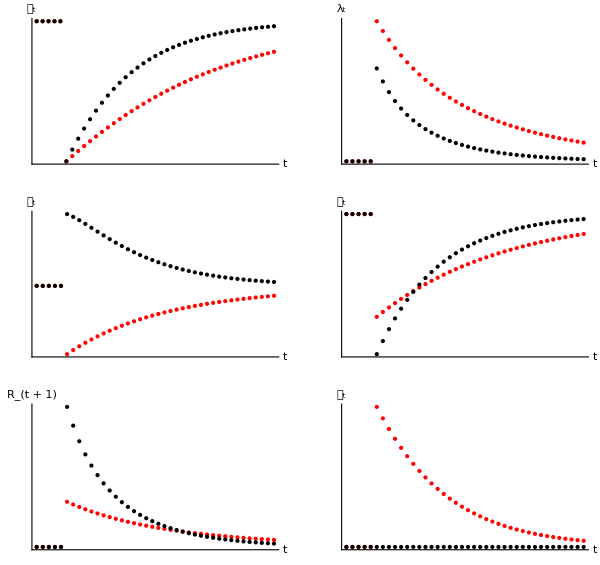

```mathematica
kDropCostAdj0VsBase=GraphicsGrid[{
{Show[𝓀TimeCostAdjBase,𝓀TimeCostAdj0],Show[λTimeCostAdjBase,λTimeCostAdj0]}
,{Show[𝒾TimeCostAdjBase,𝒾TimeCostAdj0],Show[𝒸TimeCostAdjBase,𝒸TimeCostAdj0]}
,{Show[ℝTimeCostAdjBase,ℝTimeCostAdj0],Show[𝒿TimeCostAdjBase,𝒿TimeCostAdj0]}
},ImageSize->600,PlotRange->All];
Print[kDropCostAdj0VsBase];
```

```mathematica
(* Level of investment falls because costs are scaled relative to level of k; ratio of i to k rises even with adj costs *)
```

```mathematica
Export["../../Figures/kDropCostAdj0VsBase.pdf",kDropCostAdj0VsBase];
Export["../../Figures/kDropCostAdj0VsBase.eps",kDropCostAdj0VsBase];
Export["../../Figures/kDropCostAdj0VsBase.png",kDropCostAdj0VsBase,ImageSize->{72 8.,72 8./GoldenRatio}];
```

### Permanent increase in depreciation rate

```mathematica
<<qRamseyParamsBase.m;
SolvePolFunc;
InitializeSimData;
Do[AddOnePeriod,{PreShockPeriods}];
δ=0.10;
SolvePolFunc;
Do[AddOnePeriod,{AfterShockPeriods}];
```

```mathematica
SetOptions[ListPlot,PlotStyle->{Red,PointSize[Medium]}];
DeprRiseCostAdjBase=GraphicsGrid[{
{𝓀TimeCostAdjBase=ListPlot[𝓀tList,AxesLabel->{"t","𝓀_t"},AxesOrigin->{0,0.Min[𝓀tList].95}],
λTimeCostAdjBase=ListPlot[λtList,AxesLabel->{"t","λ_t"},AxesOrigin->{0,Min[λtList].95}]},{𝒾TimeCostAdjBase=ListPlot[𝒾tList,AxesLabel->{"t","𝒾_t"},AxesOrigin->{0,0.Min[𝒾tList].9}],𝒸TimeCostAdjBase=ListPlot[𝒸tList,AxesLabel->{"t","𝒸_t"},AxesOrigin->{0,0.Min[𝒸tList].95}]},{
ℝTimeCostAdjBase=ListPlot[ℝtp1List,AxesLabel->{"t","R_(t + 1)"},AxesOrigin->{0,Min[ℝtp1List].99}],𝒿TimeCostAdjBase=ListPlot[𝒿tList,AxesLabel->{"t","𝒿_t"},AxesOrigin->{0,0}]
}},ImageSize->600];
SetOptions[ListPlot,PlotStyle->{Black,PointSize[Medium]}];
(*Print[DeprRiseCostAdjBase];
Export["../../Figures/DeprRiseCostAdjBase.pdf",DeprRiseCostAdjBase];
Export["../../Figures/DeprRiseCostAdjBase.eps",DeprRiseCostAdjBase];
Export["../../Figures/DeprRiseCostAdjBase.png",DeprRiseCostAdjBase,ImageSize->{72 8.,72 8./GoldenRatio}];*)
```

```mathematica
<<qRamseyParamsBase.m;
ω=0;
Quiet[SolvePolFunc];
InitializeSimData;
Do[AddOnePeriod,{PreShockPeriods}];
δ=0.10;ω=0;
Quiet[SolvePolFunc];
Do[AddOnePeriod,{AfterShockPeriods}];
```

```mathematica
DeprRiseCostAdj0=GraphicsGrid[{
{𝓀TimeCostAdj0=ListPlot[𝓀tList,AxesLabel->{"t","𝓀_t"},AxesOrigin->{0,0.Min[𝓀tList].95}],
λTimeCostAdj0=ListPlot[λtList,AxesLabel->{"t","λ_t"},AxesOrigin->{0,Min[λtList].95}]},{𝒾TimeCostAdj0=ListPlot[𝒾tList,AxesLabel->{"t","𝒾_t"},AxesOrigin->{0,0.Min[𝒾tList].9}],𝒸TimeCostAdj0=ListPlot[𝒸tList,AxesLabel->{"t","𝒸_t"},AxesOrigin->{0,0.Min[𝒸tList].95}]},{
ℝTimeCostAdj0=ListPlot[ℝtp1List,AxesLabel->{"t","R_(t + 1)"},AxesOrigin->{0,Min[ℝtp1List].99}],𝒿TimeCostAdj0=ListPlot[𝒿tList,AxesLabel->{"t","𝒿_t"},AxesOrigin->{0,0}]
}},ImageSize->600];(*
Print[DeprRiseCostAdj0];
Export["../../Figures/DeprRiseCostAdj0.pdf",DeprRiseCostAdj0];
Export["../../Figures/DeprRiseCostAdj0.eps",DeprRiseCostAdj0];
Export["../../Figures/DeprRiseCostAdj0.png",DeprRiseCostAdj0,ImageSize->{72 8.,72 8./GoldenRatio}];*)
```

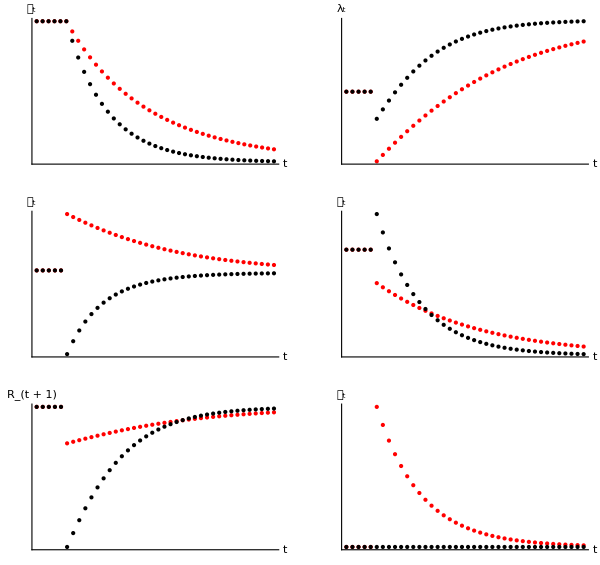

```mathematica
DeprRiseCostAdj0VsBase=GraphicsGrid[{
{Show[𝓀TimeCostAdjBase,𝓀TimeCostAdj0],Show[λTimeCostAdjBase,λTimeCostAdj0]}
,{Show[𝒾TimeCostAdjBase,𝒾TimeCostAdj0],Show[𝒸TimeCostAdjBase,𝒸TimeCostAdj0]}
,{Show[ℝTimeCostAdjBase,ℝTimeCostAdj0],Show[𝒿TimeCostAdjBase,𝒿TimeCostAdj0]}
},ImageSize->600,PlotRange->All];
Print[DeprRiseCostAdj0VsBase];
Export["../../Figures/DeprRiseCostAdj0VsBase.pdf",DeprRiseCostAdj0VsBase];
Export["../../Figures/DeprRiseCostAdj0VsBase.eps",DeprRiseCostAdj0VsBase];
Export["../../Figures/DeprRiseCostAdj0VsBase.png",DeprRiseCostAdj0VsBase,ImageSize->{72 8.,72 8./GoldenRatio}];
```

### Permanent decrease in patience

```mathematica
<<qRamseyParamsBase.m;
SolvePolFunc;
InitializeSimData;
Do[AddOnePeriod,{PreShockPeriods}];
β=0.94;
SolvePolFunc;
Do[AddOnePeriod,{AfterShockPeriods}];
```

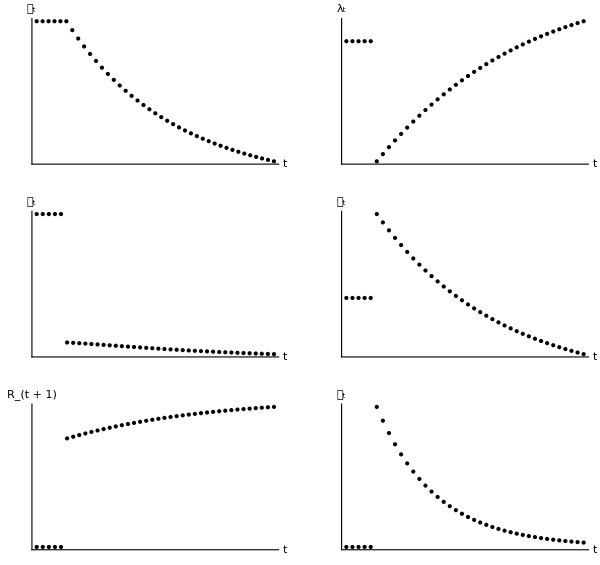

```mathematica
PatDropBase=GraphicsGrid[{
{𝓀TimeAdjCost0=ListPlot[𝓀tList,AxesLabel->{"t","𝓀_t"},AxesOrigin->{0,0. Min[𝓀tList].95}],
λTimeAdjCost0=ListPlot[λtList,AxesLabel->{"t","λ_t"},AxesOrigin->{0,Min[λtList].95}]},
{𝒾TimeAdjCost0=ListPlot[𝒾tList,AxesLabel->{"t","𝒾_t"},AxesOrigin->{0,0.Min[𝒾tList].9}],
𝒸TimeAdjCost0=ListPlot[𝒸tList,AxesLabel->{"t","𝒸_t"},AxesOrigin->{0,0.Min[𝒸tList].95}]},{ℝTimeAdjCost0=ListPlot[ℝtp1List,AxesLabel->{"t","R_(t + 1)"},AxesOrigin->{0,Min[ℝtp1List].99}],𝒿TimeAdjCost0=ListPlot[𝒿tList,AxesLabel->{"t","𝒿_t"},AxesOrigin->{0,0}]
}},ImageSize->600];
Print[PatDropBase];
```

```mathematica
Export["../../Figures/PatDrop.pdf",PatDropBase];
Export["../../Figures/PatDrop.eps",PatDropBase];
Export["../../Figures/PatDrop.png",PatDropBase,ImageSize->{72 8.,72 8./GoldenRatio}];
```